计算空间曲线(cos(t),sin(t),t^2)在各点处的切向量、曲率和挠率。

```mathematica
Clear[r,t,n];T=0;r={Cos[t],Sin[t],t^2};
r1=D[r,t];r2=D[r,{t,2}];r3=D[r,{t,3}];r12=Cross[r1,r2];
Print["r'(t)=",r1," ,κ= ",Simplify[Sqrt[r12.r12]/Sqrt[r1.r1]^3]," ,τ= ",Simplify[r12.r3/r12.r12]];
Print["在t= ",T," 处, ","r'(t)=",r1/.t->T," ,κ= ",Simplify[Sqrt[r12.r12]/Sqrt[r1.r1]^3]/.t->T," ,τ= ",Simplify[r12.r3/Sqrt[r12.r12]^3]/.t->T]
```

r'(t)={-Sin[t],Cos[t],2 t} ,κ= (√(5+4 t^2))/((1+4 t^2)^(3/2)) ,τ= (2 t)/(5+4 t^2)

在t= 0 处, r'(t)={0,1,0} ,κ= √5 ,τ= 0

计算空间曲面 z=x^2-y^2 在各点处的法向量、主曲率和基本形式。

```mathematica
Clear[r,t,n];T=0;r={x,y,x^2-y^2};rx=D[r,x];ry=D[r,y];
rxx=D[r,{x,2}];rxy=D[rx,y];ryy=D[r,{y,2}];
n=Cross[rx,ry];n=n/Sqrt[n.n];
e0=rx.rx;f0=rx.ry;g0=ry.ry;l0=rxx.n;m0=rxy.n;n0=ryy.n;
b=Simplify[(l0 g0-2m0 f0 +n0 e0)/(e0 g0-f0^2)];c=Simplify[(l0 n0-m0^2)/(e0 g0-f0^2)];
k1=Simplify[(b+Sqrt[b^2-4c])/2];k2=Simplify[(b-Sqrt[b^2-4c])/2];
Print["法向量 = ",n,"\n 主曲率 k1= ",k1," k2= ",k2,"\n 第一基本形式= (",e0,")dxdx + (",2f0,")dxdy + (",g0,")dydy",", 第二基本形式= (",l0,")dxdx + (",2m0,")dxdy + (",n0,")dydy"]
```

法向量 = {-(2 x)/(√(1+4 x^2+4 y^2)),(2 y)/(√(1+4 x^2+4 y^2)),1/(√(1+4 x^2+4 y^2))}
 主曲率 k1= 1/2 (-(8 (x^2-y^2))/((1+4 x^2+4 y^2)^(3/2))+4 √((4 x^4+x^2 (4-8 y^2)+(1+2 y^2)^2)/((1+4 x^2+4 y^2)^3))) k2= 1/2 (-(8 (x^2-y^2))/((1+4 x^2+4 y^2)^(3/2))-4 √((4 x^4+x^2 (4-8 y^2)+(1+2 y^2)^2)/((1+4 x^2+4 y^2)^3)))
 第一基本形式= (1+4 x^2)dxdx + (-8 x y)dxdy + (1+4 y^2)dydy, 第二基本形式= (2/(√(1+4 x^2+4 y^2)))dxdx + (0)dxdy + (-2/(√(1+4 x^2+4 y^2)))dydy

输入平面上 n 点 P_1,...,P_n，求点 Q 使得 ∑_(i=1)^n|P_i Q|最小。

```mathematica
l={};n=4;Clear[x,y];f=0;For[i=1,i<n,i++,point=Input[];AppendTo[l,point];f=f+Sqrt[(point[[1]]-x)^2+(point[[2]]-y)^2]];Plot3D[f,{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
l={};n=4;Clear[x,y];f=0;For[i=1,i<n,i++,point=Input[];AppendTo[l,point];f=f+(point[[1]]-x)^2+(point[[2]]-y)^2];fx=D[f,x];fy=D[f,y];Solve[{fx==0,fy==0}]
```

{{x→4/3,y→5/3}}

设动点A(t,0)，B(0,1-t)。求线段 AB 扫过区域的边长和面积。

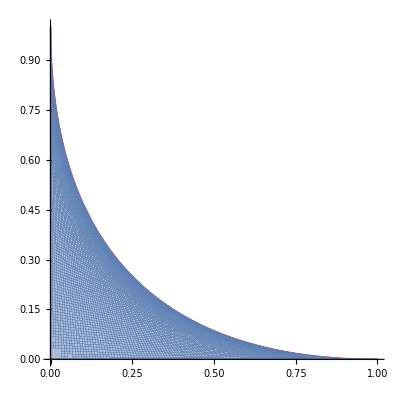

```mathematica
n=1;Clear[s,t];Show[ParametricPlot[{x,(Sqrt[n]-Sqrt[x])^2},{x,0,n},PlotStyle->{Red,Thick}],ParametricPlot[{s,n-t-s(n-t)/t},{t,0.0001,n},{s,0,t},PlotPoints->30]]
```

通过简单分析可以看出边界曲线满足：√x+√y=1

计算面积

```mathematica
Clear[x];Integrate[(Sqrt[n]-Sqrt[x])^2,{x,0,n}]
```

1/6

直观上看，如果利用最初的定义: 线段扫过的面积 去计算图中区域的面积，那么每个点都会被计算在两条线段里(这是可以直接证明的)，但是这样直接积分就涉及到了换元时的Jacobi矩阵的问题。

考虑换元(x,y)⟶ ((l×t)/(√(t^2+(n-t)^2)),(l×(1-t))/(√(t^2+(n-t)^2)))   这一换元有重要的几何意义，t是线段与x轴的交点，l是线段上点与交点的距离。

```mathematica
Clear[x,y,t,l];x=t-l*t/Sqrt[t^2+(n-t)^2];y=l (n-t)/Sqrt[t^2+(n-t)^2];jacobi=Simplify[Det[{{D[x,t],D[x,l]},{D[y,t],D[y,l]}}]];Integrate[Abs[jacobi],{t,0,n},{l,0,Sqrt[t^2+(n-t)^2]}]
```

1/3

上述计算结果也说明了，确实是这样的，每个点都被计算了两次，所以最终的总面积也是原来的两倍。

计算曲线周长：

```mathematica
Clear[r,x];r={x,(Sqrt[n]-Sqrt[x])^2};s=D[r,x];Integrate[Sqrt[s[[1]]^2+s[[2]]^2],{x,0,n}]
```

1+ArcSinh[1]/(√2)

进一步研究：设动点A(cos(t),0)，B(0,sin(t))。求线段 AB 扫过区域的边长和面积。

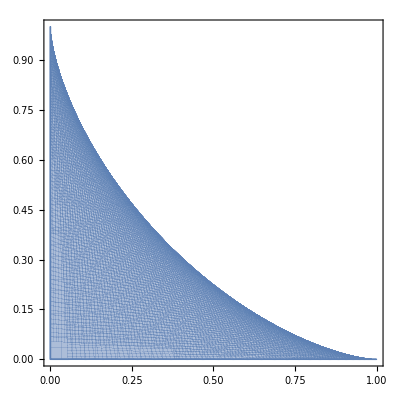

```mathematica
ParametricPlot[{s,Sin[t]-s*Tan[t]},{t,0.0001,Pi/2},{s,0,Cos[t]},PlotPoints->30]
```

```mathematica
Clear[s,t,y];y=Sin[t]-s*Tan[t];D[y,t]
```

Cos[t]-s Sec[t]^2

所以在s处的最高点满足s=cos^3(t),经过简单的化简得到如下表达式。y=(1-x^(2/3))^(3/2),即x^(2/3)+y^(2/3)=1;
以下为求对应弧长

```mathematica
y=(1-x^(2/3))^(3/2);Integrate[Sqrt[1+D[y,x]^2],{x,0,1}]
```

3/2

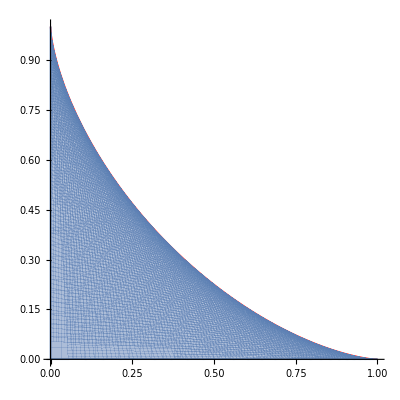

```mathematica
Show[ParametricPlot[{x,Sqrt[1-CubeRoot[x]^2]^3},{x,0,1},PlotStyle->{Red,Thick}],ParametricPlot[{s,Sin[t]-s*Tan[t]},{t,0.0001,Pi/2},{s,0,Cos[t]},PlotPoints->30]]
```

综合上述计算和观察，我们不难得出如下结论：
设动点A(s,0)，B(0,t)满足条件s^n+t^n=1(s,t∈[0,1])。则线段 AB 扫过区域与x轴y轴围成的区域的上边界满足x^(n/(n+1))+y^(n/(n+1))=1
直线方程为y=t-t/s x,对固定的x,左式对t求导

```mathematica
Clear[s,t,x,y,n];s=Surd[1-t^n,n];y=t-t x/s;Solve[D[y,t]==0]
y=Simplify[t-t*((1-t^n)^(1/n))/(1+t^n ((1-t^n)^(1/n))^-n)/s,Assumptions->{Element[n,Integers],t<1,t>0,n>0}]
x=Simplify[((1-t^n)^(1/n))/(1+t^n ((1-t^n)^(1/n))^-n),Assumptions->Element[n,Integers]]
Simplify[x^(n/(n+1))+y^(n/(n+1)),Assumptions->Element[n,Integers]]
```

{{x→((1-t^n)^(1/n))/(1+t^n ((1-t^n)^(1/n))^-n)}}

t^(1+n)/(t^n+((1-t^n)^(1/n))^n)

(((1-t^n)^(1/n))^(1+n))/(t^n+((1-t^n)^(1/n))^n)

(t^(1+n)/(t^n+((1-t^n)^(1/n))^n))^(n/(1+n))+((((1-t^n)^(1/n))^(1+n))/(t^n+((1-t^n)^(1/n))^n))^(n/(1+n))

这里不知道为什么没有化到最简式子，但是我们人工看上面这条式子会发现其实就是t^n+(1-t^n)=1

```mathematica
y=Refine[Simplify[t-t*((1-t^n)^(1/n))/(1+t^n ((1-t^n)^(1/n))^-n)/s,Assumptions->Element[n,Integers]&&t<1&&t>0&&n>0]]
```

t^(1+n)/(t^n+((1-t^n)^(1/n))^n)